# The function Table, Jacobi, and Gauss-Seidel 385-685

```mathematica
(*  In this notebook I use the function Table which I did not discuss in class. Read the page for Table in the help documentation. This is a very nice replacement for For loops at times. It is a good addition to any Mathematica developer's toolbox. Maybe you can guess what it does by evaluating the following code blocks:  *)
```

```mathematica
Table[i, {i, 1,3}]
```

{1,2,3}

```mathematica
Table[i^2, {i, 1,3}]
```

{1,4,9}

```mathematica
Table[i/2, {i, 1,3}]
```

{1/2,1,3/2}

```mathematica
Table[{i,alpha}, {i, 1,3}]
```

{{1,alpha},{2,alpha},{3,alpha}}

```mathematica
(* Some nested Tables: *)
```

```mathematica
Table[Table[j,{j,1,3}],{i, 1,3}]
```

{{1,2,3},{1,2,3},{1,2,3}}

```mathematica
Table[Table[i,{j,1,3}],{i, 1,3}]
```

{{1,1,1},{2,2,2},{3,3,3}}

```mathematica
(* Dont panic! There is a simpler notation for nested tables: Notice the order of the {i, 1, 3} {j, 1, 3}*)
```

```mathematica
Table[i,{i, 1,3},{j,1,3}]
```

{{1,1,1},{2,2,2},{3,3,3}}

```mathematica
Table[j,{i, 1,3},{j,1,3}]
```

{{1,2,3},{1,2,3},{1,2,3}}

```mathematica
Table[
Table[{i,j},{j,1,3}],
 {i, 1,3}
]
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}}}

```mathematica
Table[
Table[i + j ,{j,1,3}],
 {i, 1,3}
]
```

{{2,3,4},{3,4,5},{4,5,6}}

```mathematica
Table[
Table[3*(i-1) + j ,{j,1,3}],
 {i, 1,3}
]
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
(* i goes from 0 to 2  (rows ) (j goes from 1 to 3)  *)
```

```mathematica
mat = Table[3*i + j,{i, 0,2},{j,1,3}]
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
MatrixForm[mat]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
(* This eliminates those nasty append to [matrix, newrow]. *)
```

```mathematica
A = Table[Subscript[a, i,j],{i,10},{j,10}];
```

```mathematica
MatrixForm[LowerTriangularize[A,0]]
```

(a_(1,1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a_(2,1) | a_(2,2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a_(3,1) | a_(3,2) | a_(3,3) | 0 | 0 | 0 | 0 | 0 | 0 | 0
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4) | 0 | 0 | 0 | 0 | 0 | 0
a_(5,1) | a_(5,2) | a_(5,3) | a_(5,4) | a_(5,5) | 0 | 0 | 0 | 0 | 0
a_(6,1) | a_(6,2) | a_(6,3) | a_(6,4) | a_(6,5) | a_(6,6) | 0 | 0 | 0 | 0
a_(7,1) | a_(7,2) | a_(7,3) | a_(7,4) | a_(7,5) | a_(7,6) | a_(7,7) | 0 | 0 | 0
a_(8,1) | a_(8,2) | a_(8,3) | a_(8,4) | a_(8,5) | a_(8,6) | a_(8,7) | a_(8,8) | 0 | 0
a_(9,1) | a_(9,2) | a_(9,3) | a_(9,4) | a_(9,5) | a_(9,6) | a_(9,7) | a_(9,8) | a_(9,9) | 0
a_(10,1) | a_(10,2) | a_(10,3) | a_(10,4) | a_(10,5) | a_(10,6) | a_(10,7) | a_(10,8) | a_(10,9) | a_(10,10))

```mathematica
(* Here is an Identity Matrix of Dim 10*)
```

```mathematica
MatrixForm[IdentityMatrix[10]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(* Here is a 10 by 10 matrix of with random real entries between 0 and 100 *)
```

```mathematica
MatrixForm[RandomReal[{0,100},{10,10}]]
```

(65.0679 | 57.8626 | 64.3283 | 6.84704 | 6.85407 | 38.9266 | 88.8263 | 0.487598 | 90.5042 | 14.3631
0.739168 | 19.834 | 35.4565 | 96.6746 | 16.545 | 17.9652 | 57.0502 | 89.8395 | 92.5016 | 93.647
22.6856 | 95.4723 | 82.7052 | 33.4894 | 1.6775 | 96.9838 | 76.3633 | 88.228 | 58.8989 | 56.8329
50.3136 | 17.6078 | 65.0901 | 28.3992 | 17.1947 | 16.098 | 98.8783 | 96.7286 | 16.7813 | 26.1053
65.0565 | 14.8396 | 45.9934 | 46.1289 | 97.0199 | 85.3261 | 73.8948 | 43.4826 | 66.4098 | 66.1692
83.3153 | 3.58697 | 94.7945 | 73.3204 | 70.5114 | 55.6758 | 50.4139 | 70.0013 | 60.6109 | 69.9761
39.5229 | 57.7821 | 78.3159 | 42.0803 | 87.8928 | 67.6244 | 0.424569 | 52.724 | 36.9102 | 47.0029
30.0646 | 42.8279 | 97.9717 | 65.5928 | 43.1892 | 63.8947 | 98.5321 | 62.0828 | 19.4562 | 63.8107
53.8585 | 98.3274 | 5.22041 | 75.1724 | 85.0461 | 67.8217 | 70.5785 | 19.9534 | 2.65985 | 31.8817
6.94469 | 39.4564 | 72.3264 | 44.4681 | 76.5028 | 59.9225 | 42.3299 | 74.4864 | 68.8807 | 54.8138)

# Jacobi

```mathematica
(* Here is the A matrix as described in the chapter: *)
```

```mathematica
A = Table[If[i - j == 1 || j - i == 1,.25,If[i == j, .5,0]],{i,50},{j,50}];
```

```mathematica
MatrixForm[A]
```

(0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5)

```mathematica
(*Here is the Jacobi estimated inverse: *)
```

```mathematica
B = Table[If[i == j, 2,0],{i,50},{j,50}];
MatrixForm[B]
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2)

```mathematica
id= IdentityMatrix[50];
```

```mathematica
(* Here is the largest eigenvalue: (Notice it is very close to 1): *)
```

```mathematica
SetPrecision[Max[Eigenvalues[id - A.B]],70]
```

0.99810332873704410427961875029723159968852996826171875

```mathematica
(*Power method 50 iterations*)
```

```mathematica
x0= Table[1,{i, 50}];
sigma = id - A.B;
For[i =1, i ≤ 50,i++,
x0 = sigma.x0/Norm[sigma.x0]
];
```

```mathematica
SetPrecision[Norm[sigma.x0]/Norm[x0],70]
```

0.9977347761818660121235780025017447769641876220703125

```mathematica
(*500 iterations now it is the same up to the 10th digit as the computed value by Eigenvalues[]*)
```

```mathematica
x0= Table[1,{i, 50}];
sigma = id - A.B;
For[i =1, i ≤ 500,i++,
x0 = sigma.x0/Norm[sigma.x0]
];
```

```mathematica
SetPrecision[Norm[sigma.x0]/Norm[x0],70]
```

0.99810332828357239964844893620465882122516632080078125

```mathematica
(*5000 iterations *)
```

```mathematica
x0= Table[1,{i, 50}];
sigma = id - A.B;
For[i =1, i ≤ 5000,i++,
x0 = sigma.x0/Norm[sigma.x0]
];
```

```mathematica
SetPrecision[Norm[sigma.x0]/Norm[x0],70]
```

0.99810332873704410427961875029723159968852996826171875

```mathematica
(* our initial b vector: *)
```

```mathematica
b = Table[1/i,{i, 50}]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19,1/20,1/21,1/22,1/23,1/24,1/25,1/26,1/27,1/28,1/29,1/30,1/31,1/32,1/33,1/34,1/35,1/36,1/37,1/38,1/39,1/40,1/41,1/42,1/43,1/44,1/45,1/46,1/47,1/48,1/49,1/50}

```mathematica
(* our initial solution x0: Basically just initializing a vector of the appropriate length: *)
```

```mathematica
x'= Table[1,{i, 50}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(* The first 50 iterations:*)
```

```mathematica
For[i = 1, i ≤ 50, ++i, 
r = b - A.x';
x' = x' + B.r
]
```

```mathematica
x'
```

{2.64199,-0.917622,1.93728,-0.546301,1.59719,-0.121168,1.36795,0.242796,1.2107,0.520313,1.10879,0.71407,1.04818,0.838977,1.01582,0.913652,1.00083,0.955239,0.995299,0.976968,0.994197,0.98775,0.99475,0.992913,0.995606,0.995267,0.996097,0.995997,0.995665,0.995169,0.993366,0.991825,0.987388,0.983773,0.974566,0.967228,0.950014,0.93662,0.907156,0.884891,0.838442,0.804597,0.736919,0.68982,0.598425,0.538483,0.423778,0.354236,0.220025,0.146971}

```mathematica
(* Using gaussian elimination to obtain an actual inverse: *)
```

```mathematica
x = LinearSolve[A,b]
```

{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}

```mathematica
(* Normed residual error: *)
```

```mathematica
Norm[x - x']/Norm[x]
```

0.120834 √(Abs[-1.59862-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-1.59793-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-1.55915-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-1.50449-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-1.46598-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-1.44175-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-1.37435-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-1.30402-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-1.23173-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-1.15806-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-1.08339-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-1.00797-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-0.931965-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-0.855506-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-0.778683-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-0.701563-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-0.624198-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-0.54663-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-0.46889-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-0.391005-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-0.312994-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-0.234875-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-0.156662-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[-0.0783673-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[4.0817×10^-16-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[0.08-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[0.160068-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[0.240213-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[0.320446-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[0.40078-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[0.481229-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[0.561814-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[0.642557-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[0.723487-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[0.804639-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[0.88606-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[0.96781-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[1.04997-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[1.13264-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[1.21596-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[1.30016-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[1.38552-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[1.47252-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[1.5619-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[1.65494-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[1.75404-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[1.86425-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[1.99828-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[2.19897-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2+Abs[2.73299-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}']^2)

```mathematica
(*Computing without the norm function: *)
```

```mathematica
Sqrt[Total[(x - x')^2]]/Sqrt[Total[x^2]]
```

0.120834 √((-1.59862-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-1.59793-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-1.55915-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-1.50449-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-1.46598-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-1.44175-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-1.37435-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-1.30402-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-1.23173-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-1.15806-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-1.08339-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-1.00797-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-0.931965-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-0.855506-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-0.778683-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-0.701563-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-0.624198-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-0.54663-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-0.46889-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-0.391005-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-0.312994-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-0.234875-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-0.156662-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(-0.0783673-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(4.0817×10^-16-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(0.08-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(0.160068-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(0.240213-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(0.320446-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(0.40078-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(0.481229-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(0.561814-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(0.642557-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(0.723487-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(0.804639-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(0.88606-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(0.96781-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(1.04997-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(1.13264-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(1.21596-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(1.30016-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(1.38552-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(1.47252-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(1.5619-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(1.65494-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(1.75404-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(1.86425-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(1.99828-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(2.19897-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2+(2.73299-{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}')^2)

```mathematica
(*After 500 iterations: reinitialize b and x' ... *)
```

```mathematica
b = Table[1/i,{i, 50}];
x'= Table[1,{i, 50}];
For[i = 1, i ≤ 500, ++i, 
r = b - A.x' ;
x' = x' + B.r;
]
```

```mathematica
Norm[x - x']/Norm[x]
```

0.411436

```mathematica
(*After 5000 iterations: reinitialize b and x' ... *)
```

```mathematica
b = Table[1/i,{i, 50}];
x'= Table[1,{i, 50}];
For[i = 1, i ≤ 5000, ++i, 
r = b - A.x' ;
x' = x' + B.r;
]
```

```mathematica
Norm[x - x']/Norm[x]
```

0.0000801626

```mathematica
(* Starting with x0=(1,1,...,1) we have relative normed error of 1.101438 after 50 iterations, 0.41144 after 500 iterations, and 8x10^-5 after 5000 iterations.   *)
```

# Gauss-Seidel

```mathematica
A = Table[If[i - j == 1 || j - i == 1,.25,If[i == j, .5,0]],{i,50},{j,50}];
```

```mathematica
MatrixForm[A]
```

(0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5 | 0.25
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.25 | 0.5)

```mathematica
l = LowerTriangularize[A,0];

(* Keep the same format as for jacobi just using the Built in Inverse function instead of forward substitution: 

"Repeating the prior example for this case, the spectral radius of  
I-BA is 0.996. Nearly the same as for the Jacobi method. However, this time the relative normed error is 

0.6438 for 50 iterations,
 0.1102 for 500 and 
4x10^-9, for 5,000.

 These results are orders of magnitude better. It is not surprising that the Gauss-Seidel method is preferred." 
"*)
```

```mathematica
(* Need to use the power method for Gauss Seidel: Because it has complex eigenvalues *)
```

```mathematica
sigma = IdentityMatrix[50] - A.Inverse[l];
Max[Eigenvalues[sigma]]
```

Max::nord: Invalid comparison with -0.0923504-0.0106031 ⅈ attempted.

Max::nord: Invalid comparison with -0.0923504+0.0106031 ⅈ attempted.

Max::nord: Invalid comparison with -0.0879284-0.0313771 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Max[-0.0923504-0.0106031 ⅈ,-0.0923504+0.0106031 ⅈ,-0.0879284-0.0313771 ⅈ,-0.0879284+0.0313771 ⅈ,-0.0792769-0.0509461 ⅈ,-0.0792769+0.0509461 ⅈ,-0.0665965-0.0686516 ⅈ,-0.0665965+0.0686516 ⅈ,-0.0500515-0.0837555 ⅈ,-0.0500515+0.0837555 ⅈ,-0.0299699-0.095351 ⅈ,-0.0299699+0.095351 ⅈ,-0.00699885-0.102518 ⅈ,-0.00699885+0.102518 ⅈ,0.0179469-0.104513 ⅈ,0.0179469+0.104513 ⅈ,0.0438377-0.100805 ⅈ,0.0438377+0.100805 ⅈ,0.0695931-0.0909657 ⅈ,0.0695931+0.0909657 ⅈ,0.0939544-0.074579 ⅈ,0.0939544+0.074579 ⅈ,0.115388-0.0513345 ⅈ,0.115388+0.0513345 ⅈ,0.132728-0.0211608 ⅈ,0.132728+0.0211608 ⅈ,0.99621+0. ⅈ]

```mathematica
(*Using the power method we obtain eigenvalues as displayed in the book: Notice that .996 is only very slightly less than .998 the max eig for Jacobi but gauss seidel performs much better: *)
```

```mathematica
sigma = id - A.Inverse[l];
x0= Table[1,{i, 50}];
For[i =1, i ≤ 50,i++,
x0 = sigma.x0/Norm[sigma.x0]
];
SetPrecision[Norm[sigma.x0]/Norm[x0],70]
```

0.98298786477153754503888194449245929718017578125

```mathematica
(* by 500 we get the right eigenvalue: *)
```

```mathematica
sigma = id - A.Inverse[l];
x0= Table[1,{i, 50}];
For[i =1, i ≤ 500,i++,
x0 = sigma.x0/Norm[sigma.x0]
];
SetPrecision[Norm[sigma.x0]/Norm[x0],70]
```

0.99612051161324455250678511220030486583709716796875

```mathematica
sigma = id - A.Inverse[l];
x0= Table[1,{i, 50}];
For[i =1, i ≤ 500,i++,
x0 = sigma.x0/Norm[sigma.x0]
];
SetPrecision[Norm[sigma.x0]/Norm[x0],70]
```

0.99612051161324455250678511220030486583709716796875

```mathematica
(* Here is a plot of the computed eigenvalues from the powermethod by iteration count: notice that 5000 is waaaaaay overkill.*)
```

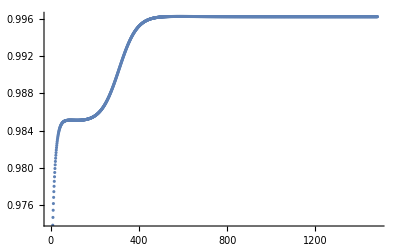

```mathematica
eigs = {};
For[j = 20, j ≤ 1500, j++,
sigma = id - A.Inverse[l];
x0= Table[1,{i, 50}];
For[i =1, i ≤ j,i++,
x0 = sigma.x0/Norm[sigma.x0]
];
AppendTo[eigs, SetPrecision[Norm[sigma.x0]/Norm[x0],70]]
]
ListPlot[eigs]
```

```mathematica
(* Computation using Gauss-seidel   *)
```

```mathematica
(* error : 0.6438 for 50 iterations, *)
```

```mathematica
b = Table[1/i,{i, 50}];
x = LinearSolve[A,b];
x'= Table[1,{i, 50}];

For[i = 1, i ≤ 50, ++i, 
r = b - A.x' ;
x' = x' + Inverse[l].r;
]
```

```mathematica
Norm[x - x']/Norm[x]
```

0.643862

```mathematica
(* error : 0.1102 for 500 *)
```

```mathematica
b = Table[1/i,{i, 50}];
x = LinearSolve[A,b];
x'= Table[1,{i, 50}];

For[i = 1, i ≤ 500, ++i, 
r = b - A.x' ;
x' = x' + Inverse[l].r;
]
```

```mathematica
Norm[x - x']/Norm[x]
```

0.1102

```mathematica
(* error :  4x10^-9, for 5,000  *)
```

```mathematica
b = Table[1/i,{i, 50}];
x = LinearSolve[A,b];
x'= Table[1,{i, 50}];

For[i = 1, i ≤ 5000, ++i, 
r = b - A.x' ;
x' = x' + Inverse[l].r;
]
```

```mathematica
Norm[x - x']/Norm[x]
```

4.18468×10^-9

```mathematica
(* Now using forward substitution: I used xhat for x' here *)
```

```mathematica
b = Table[1/i,{i, 50}];
x = LinearSolve[A,b];
xhat= Table[1,{i, 50}];
For[k = 1, k ≤ 50, ++k, 
r = b - A.xhat ;
bh =  l.xhat + r;

For[i = 1, i ≤ Length[bh],i++, 
If[i == 1,
xhat[[i]] = bh[[i]]/l[[i,i]],
xhat[[i]] =(1/l[[i,i]] )* ( bh[[i]] - ∑_(j =1)^(i - 1) l[[i,j]]*xhat[[i-1]]);
   ];
   ];
 ];
```

```mathematica
x
```

{2.73299,-1.46598,2.19897,-1.59862,1.99828,-1.59793,1.86425,-1.55915,1.75404,-1.50449,1.65494,-1.44175,1.5619,-1.37435,1.47252,-1.30402,1.38552,-1.23173,1.30016,-1.15806,1.21596,-1.08339,1.13264,-1.00797,1.04997,-0.931965,0.96781,-0.855506,0.88606,-0.778683,0.804639,-0.701563,0.723487,-0.624198,0.642557,-0.54663,0.561814,-0.46889,0.481229,-0.391005,0.40078,-0.312994,0.320446,-0.234875,0.240213,-0.156662,0.160068,-0.0783673,0.08,4.0817×10^-16}

```mathematica
xhat
```

{2.61334,-1.22981,1.85079,-1.14416,1.44429,-0.952008,1.13462,-0.754471,0.88322,-0.576491,0.67864,-0.425805,0.514616,-0.303622,0.385735,-0.208035,0.286622,-0.135628,0.211996,-0.082423,0.156904,-0.0444641,0.116933,-0.018153,0.0883187,-0.000416172,0.0679831,0.0112467,0.053495,0.0187846,0.0430041,0.0236521,0.0351564,0.0268833,0.029007,0.0291697,0.0239338,0.0309394,0.019554,0.0324335,0.0156475,0.0337747,0.012091,0.0350236,0.00880804,0.0362179,0.00573815,0.037393,0.00282216,0.0385889}

```mathematica
Norm[x - xhat]/Norm[x]
```

0.643862

```mathematica
b = Table[1/i,{i, 50}];
x = LinearSolve[A,b];
xhat= Table[1,{i, 50}];
For[k = 1, k ≤ 500, ++k, 
r = b - A.xhat ;
bh =  l.xhat + r;

For[i = 1, i ≤ Length[bh],i++, 
If[i == 1,
xhat[[i]] = bh[[i]]/l[[i,i]],
xhat[[i]] =(1/l[[i,i]] )* ( bh[[i]] - ∑_(j =1)^(i - 1) l[[i,j]]*xhat[[i-1]]);
   ];
   ];
 ];
```

```mathematica
Norm[x - xhat]/Norm[x]
```

0.1102

```mathematica
b = Table[1/i,{i, 50}];
x = LinearSolve[A,b];
xhat= Table[1,{i, 50}];
For[k = 1, k ≤ 5000, ++k, 
r = b - A.xhat ;
bh =  l.xhat + r;

For[i = 1, i ≤ Length[bh],i++, 
If[i == 1,
xhat[[i]] = bh[[i]]/l[[i,i]],
xhat[[i]] =(1/l[[i,i]] )* ( bh[[i]] - ∑_(j =1)^(i - 1) l[[i,j]]*xhat[[i-1]]);
   ];
   ];
 ];
```

```mathematica
Norm[x - xhat]/Norm[x]
```

4.18468×10^-9